```mathematica
Solve[{0==s*(y-x),0==r*x-y-x*z,0==-b*z+x*y},{x,y,z}]
```

{{x→0,y→0,z→0},{x→-√b √(-1+r),y→-√b √(-1+r),z→-1+r},{x→√b √(-1+r),y→√b √(-1+r),z→-1+r}}

```mathematica
DSolve[z'[t]==-b*z[t],z[t],t]
```

{{z[t]→ⅇ^(-b t) C[1]}}

```mathematica
DSolve[{x'[t]==s*(y[t]-x[t]),y'[t]==r*x[t]-y[t]},{x[t],y[t]},t]//FullSimplify
```

{{x[t]→(ⅇ^(-1/2 (1+s+√(1+s (-2+4 r+s))) t) ((-1+s+√(1+s (-2+4 r+s))+ⅇ^(√(1+s (-2+4 r+s)) t) (1-s+√(1+s (-2+4 r+s)))) C[1]+2 (-1+ⅇ^(√(1+s (-2+4 r+s)) t)) s C[2]))/(2 √(1+s (-2+4 r+s))),y[t]→(ⅇ^(-1/2 (1+s+√(1+s (-2+4 r+s))) t) (2 (-1+ⅇ^(√(1+s (-2+4 r+s)) t)) r C[1]+(1-s+√(1+s (-2+4 r+s))+ⅇ^(√(1+s (-2+4 r+s)) t) (-1+s+√(1+s (-2+4 r+s)))) C[2]))/(2 √(1+s (-2+4 r+s)))}}

```mathematica
(ⅇ^(-1/2 (1+s+√(1+s (-2+4 r+s))) t) ((-1+s+√(1+s (-2+4 r+s))+ⅇ^(√(1+s (-2+4 r+s)) t) (1-s+√(1+s (-2+4 r+s)))) C[1]+2 (-1+ⅇ^(√(1+s (-2+4 r+s)) t)) s C[2]))/(2 √(1+s (-2+4 r+s)))/.{√(1+s (-2+4 r+s))->Δ}//FullSimplify
```

(ⅇ^(-1/2 t (1+s+Δ)) ((-1+s+Δ+ⅇ^(t Δ) (1-s+Δ)) C[1]+2 (-1+ⅇ^(t Δ)) s C[2]))/(2 √(1+s (-2+4 r+s)))

```mathematica
(s+1)^2-4*s*(1-r)//FullSimplify
```

1+s (-2+4 r+s)

```mathematica
DSolve[-η*v''[z]==ρ*g*Sin[θ],v[z],z]//FullSimplify
```

{{v[z]→C[1]+z C[2]-(g z^2 ρ Sin[θ])/(2 η)}}

```mathematica
C[1]+z C[2]+(g z^2 ρ Sin[θ])/(2 η)//TeXForm
```

\frac{g \rho  z^2 \sin (\theta )}{2 \eta }+c_2 z+c_1

```mathematica
DSolve[{-η*v''[z]==ρ*g*Sin[θ],v[0]==0,v'[h]==0},v[z],z]//FullSimplify
```

{{v[z]→(g (2 h-z) z ρ Sin[θ])/(2 η)}}

```mathematica
Series[Sin[θ],{θ,2*Pi,5}]//FullSimplify
```

(θ-2 π)-1/6 (θ-2 π)^3+1/120 (θ-2 π)^5+O[θ-2 π]^6

```mathematica
(*n even*)
```

```mathematica
DSolve[θ''[t]==-(θ[t]-n*Pi),θ[t],t]
```

{{θ[t]→n π+C[1] Cos[t]+C[2] Sin[t]}}

```mathematica
(*n odd*)
```

```mathematica
DSolve[θ''[t]==(θ[t]-n*Pi),θ[t],t]
```

{{θ[t]→n π+ⅇ^t C[1]+ⅇ^-t C[2]}}

```mathematica
D[n π+ⅇ^t C[1]+ⅇ^-t C[2],t]
```

ⅇ^t C[1]-ⅇ^-t C[2]

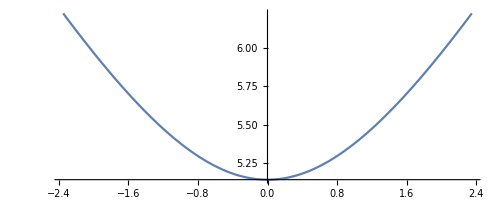

```mathematica
ParametricPlot[{ⅇ^t -ⅇ^-t ,π+ⅇ^t+ⅇ^-t},{t,-1,1}]
```

```mathematica
(*n even, oscillation*)
```

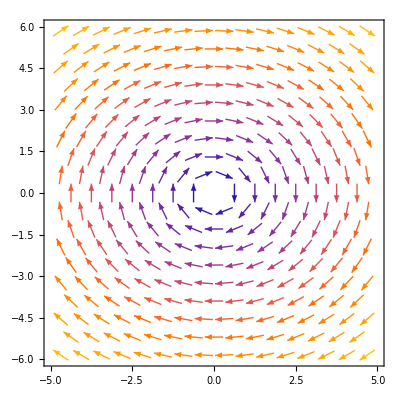

```mathematica
VectorPlot[{y,-(x-0Pi)},{x,-5,5},{y,-6,6}]
```

```mathematica
(*n odd, saddle point*)
```

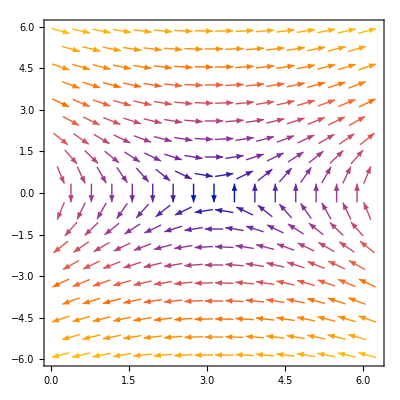

```mathematica
VectorPlot[{y,+(x-1Pi)},{x,0,6.28},{y,-6,6}]
```

```mathematica
(*n even, with q*)
```

```mathematica
DSolve[θ''[t]==-(1/q)*θ'[t]-(θ[t]-n*Pi),θ[t],t]
```

{{θ[t]→n π+ⅇ^(1/2 (-√(-4+1/q^2)-1/q) t) C[1]+ⅇ^(1/2 (√(-4+1/q^2)-1/q) t) C[2]}}

```mathematica
(*n odd, with q*)
```

```mathematica
DSolve[θ''[t]==-(1/q)*θ'[t]+(θ[t]-n*Pi),θ[t],t]
```

{{θ[t]→n π+ⅇ^(1/2 (-√(4+1/q^2)-1/q) t) C[1]+ⅇ^(1/2 (√(4+1/q^2)-1/q) t) C[2]}}

```mathematica
(*underdamped*)
```

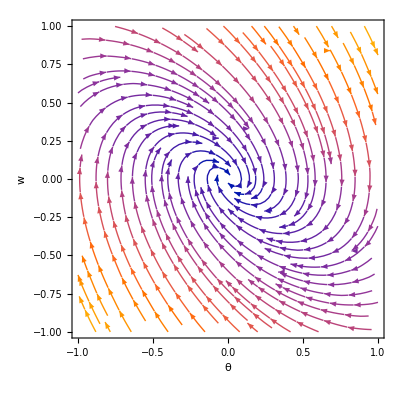

```mathematica
StreamPlot[{y,-1/(1/1)*y-(x-0Pi)},{x,-1,1},{y,-1,1},FrameLabel->{"θ","w"}]
```

```mathematica
(*Overdamped*)
```

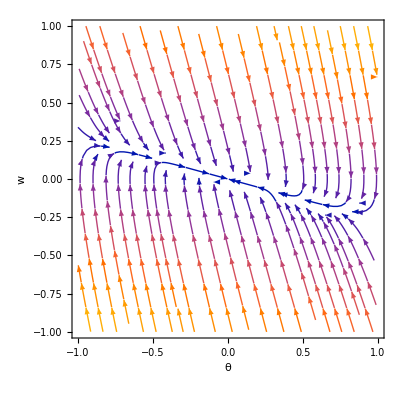

```mathematica
StreamPlot[{y,-1/(1/4)*y-(x-0Pi)},{x,-1,1},{y,-1,1},FrameLabel->{"θ","w"}]
```

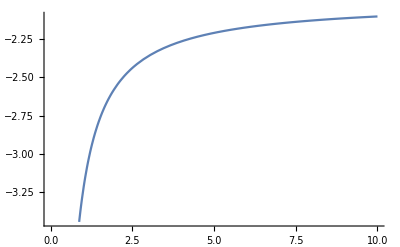

```mathematica
Plot[-Sqrt[1/q^2+4]-1/q,{q,0,10}]
```

```mathematica
dw=D[n π+ⅇ^(1/2 (-√(4+1/q^2)-1/q) t) C[1]+ⅇ^(1/2 (√(4+1/q^2)-1/q) t) C[2],{t,2}]
```

1/4 ⅇ^(1/2 (-√(4+1/q^2)-1/q) t) (-√(4+1/q^2)-1/q)^2 C[1]+1/4 ⅇ^(1/2 (√(4+1/q^2)-1/q) t) (√(4+1/q^2)-1/q)^2 C[2]

```mathematica
dθ=D[n π+ⅇ^(1/2 (-√(4+1/q^2)-1/q) t) C[1]+ⅇ^(1/2 (√(4+1/q^2)-1/q) t) C[2],t]
```

1/2 ⅇ^(1/2 (-√(4+1/q^2)-1/q) t) (-√(4+1/q^2)-1/q) C[1]+1/2 ⅇ^(1/2 (√(4+1/q^2)-1/q) t) (√(4+1/q^2)-1/q) C[2]

```mathematica
Limit[dw/dθ,t->Infinity]//FullSimplify
```

ConditionalExpression[1/2 (√(4+1/q^2)-1/q), (C[1]|C[2])∈ℝ&&q+√(4+1/q^2) q^2>0]